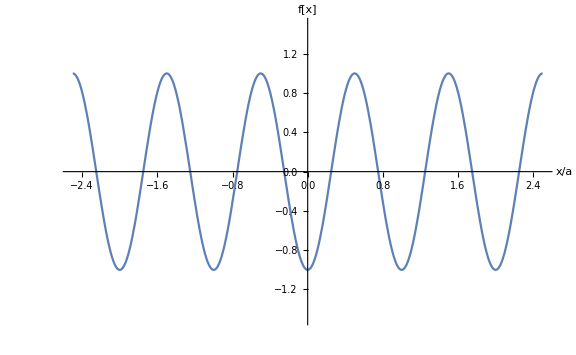

```mathematica
f[x_] := -Cos[2π x];
Plot[f[x], {x,-5/2, 5/2}, PlotRange->{-1.5, 1.5}, ImageSize->Large, AxesLabel->{"x/a", "f[x]"}]
```

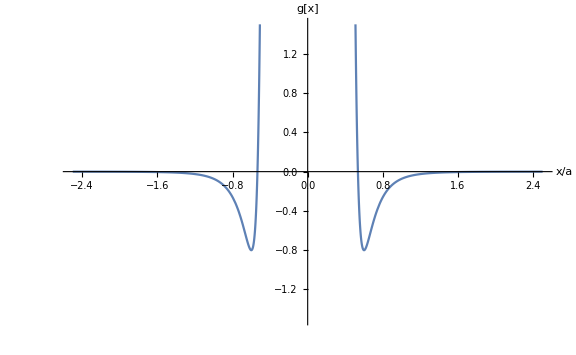

```mathematica
rm = 0.6;
ϵ = 0.8;
g[x_] := ϵ((rm/x)^12-2(rm/x)^6);
Plot[g[x], {x, -5/2, 5/2}, PlotRange->{-1.5, 1.5}, ImageSize->Large,  AxesLabel->{"x/a", "g[x]"}]
```

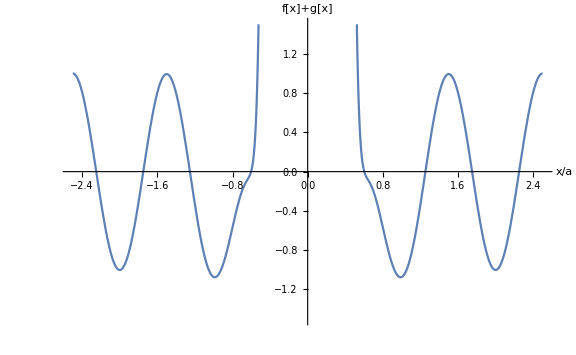

```mathematica
Plot[f[x]+g[x], {x, -5/2, 5/2}, PlotRange->{-1.5, 1.5}, ImageSize->Large,  AxesLabel->{"x/a", "f[x]+g[x]"}]
```

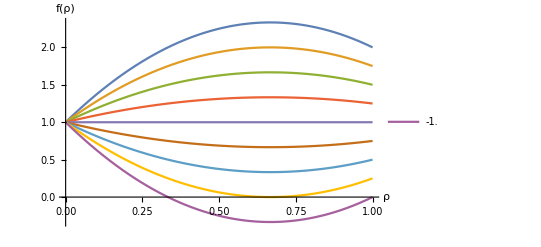

```mathematica
tab = Table[1-ζ(4-3ρ)ρ, {ζ, -1, 1, 0.25}];
tab2 = Table[ζ, {ζ, -1, 1, 0.25}];
Plot[tab, {ρ, 0, 1}, AxesLabel->{"ρ", "f(ρ)"}, PlotLegends->tab2]
```

```mathematica
tab
```

{1+1. (4-3 ρ) ρ,1+0.6 (4-3 ρ) ρ,1+0.2 (4-3 ρ) ρ,1-0.2 (4-3 ρ) ρ,1-0.6 (4-3 ρ) ρ,1-1. (4-3 ρ) ρ}

```mathematica
Rasterize[Plot[Evaluate[tab], {ρ, 0, 1}, PlotLegends->tab2"=ζ",  AxesLabel->{"ρ", "f(ρ)"}, ImageSize->1000], ImageResolution->100]
```

-Graphics-

```mathematica
Integrate[1-ζ ρ(4-3ρ), ρ]
```

ρ-2 ζ ρ^2+ζ ρ^3